Weather simulation using a Markov State model. Given a state transition matrix , the probability on day  is given by .
Based on Steve Brunton’s excellent “Gentle introduction to Modeling with Matrices and Vectors: A probabilistic weather model” at https://www.youtube.com/watch?v=K-8F_zDMDUI

The parameters to the model are , the state transition matrix and , the initial state.  Then the probability distribution of the state on day  is stored in . You can see more background on the maths of the model in the README.md

```mathematica
A=({{0.5, 0.5, 0.25}, {0.25, 0, 0.25}, {0.25, 0.5, 0.5}});
x[0]=({{1}, {0}, {0}});
x[t_]:=A . x[t-1];
n=25;
x[n] // TraditionalForm
```

(0.4
0.2
0.4)

The final prediction is . Notice that like maxima, we can specify the model directly as a recurrence relation and then just request the state on the final day and it will compute all the states of the model required to get there. Check the quality of convergence by the difference between the last two steps (smaller is better).

```mathematica
convergence=Max[Abs[x[n]-x[n-1]]]
```

1.77636×10^-15

...ok that’s pretty dang small. From what we know about MSMs, they should converge such that the steady state probability lies on the eigenvector corresponding to the eigenvalue 1. It’s easiest to show this if it is normalised such that its components add up to 1.

```mathematica
{eivals,eivects}=Eigensystem[A];
eivals[[1]]
eivects[[1]]
```

1.

{-0.666667,-0.333333,-0.666667}

```mathematica
eivects[[1]]/Total[eivects[[1]]]
```

{0.4,0.2,0.4}

OK cool. This is the normalised eigenvector probability distribution we computed by hand in the README and also the value returned by the convergence of the simulation. Now we plot it something like this

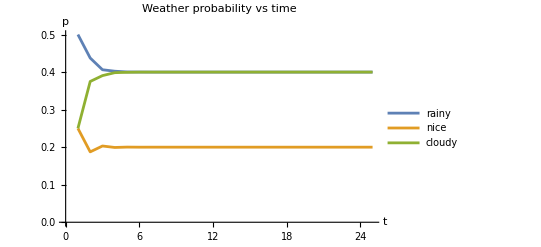

```mathematica
rainy=Flatten[(x[#][[1]])& /@ Range[n]];
nice=Flatten[(x[#][[2]])& /@ Range[n]];
cloudy=Flatten[(x[#][[3]])& /@ Range[n]];
ListPlot[{rainy,nice,cloudy},
AxesLabel->{"t","p"},
PlotLegends->{"rainy","nice","cloudy"},
Joined->True,
PlotLabel->"Weather probability vs time"
]
```